```mathematica
v={{0.,-0.04,-0.04,-0.04,-0.04,-0.02,-0.02,-0.02,-0.02},{-0.04,0.,0.,-0.02,-0.02,-0.04,0.,-0.04,0.},{-0.04,0.,0.,-0.02,-0.02,0.,-0.04,0.,-0.04},{-0.04,-0.02,-0.02,0.,0.,-0.04,0.,0.,-0.04},{-0.04,-0.02,-0.02,0.,0.,0.,-0.04,-0.04,0.},{-0.02,-0.04,0.,-0.04,0.,0.,0.,0.,0.},{-0.02,0.,-0.04,0.,-0.04,0.,0.,0.,0.},{-0.02,-0.04,0.,0.,-0.04,0.,0.,0.,0.},{-0.02,0.,-0.04,-0.04,0.,0.,0.,0.,0.}};
```

```mathematica
k=DiagonalMatrix[{x^2+y^2,(x+1)^2+y^2,(x-1)^2+y^2,x^2+(y+1)^2,x^2+(y-1)^2,(x+1)^2+(y+1)^2,(x-1)^2+(y-1)^2,(x+1)^2+(y-1)^2,(x-1)^2+(y+1)^2}]
```

{{x^2+y^2,0,0,0,0,0,0,0,0},{0,(1+x)^2+y^2,0,0,0,0,0,0,0},{0,0,(-1+x)^2+y^2,0,0,0,0,0,0},{0,0,0,x^2+(1+y)^2,0,0,0,0,0},{0,0,0,0,x^2+(-1+y)^2,0,0,0,0},{0,0,0,0,0,(1+x)^2+(1+y)^2,0,0,0},{0,0,0,0,0,0,(-1+x)^2+(-1+y)^2,0,0},{0,0,0,0,0,0,0,(1+x)^2+(-1+y)^2,0},{0,0,0,0,0,0,0,0,(-1+x)^2+(1+y)^2}}

```mathematica
h=k+v
```

{{0.+x^2+y^2,-0.04,-0.04,-0.04,-0.04,-0.02,-0.02,-0.02,-0.02},{-0.04,0.+(1+x)^2+y^2,0.,-0.02,-0.02,-0.04,0.,-0.04,0.},{-0.04,0.,0.+(-1+x)^2+y^2,-0.02,-0.02,0.,-0.04,0.,-0.04},{-0.04,-0.02,-0.02,0.+x^2+(1+y)^2,0.,-0.04,0.,0.,-0.04},{-0.04,-0.02,-0.02,0.,0.+x^2+(-1+y)^2,0.,-0.04,-0.04,0.},{-0.02,-0.04,0.,-0.04,0.,0.+(1+x)^2+(1+y)^2,0.,0.,0.},{-0.02,0.,-0.04,0.,-0.04,0.,0.+(-1+x)^2+(-1+y)^2,0.,0.},{-0.02,-0.04,0.,0.,-0.04,0.,0.,0.+(1+x)^2+(-1+y)^2,0.},{-0.02,0.,-0.04,-0.04,0.,0.,0.,0.,0.+(-1+x)^2+(1+y)^2}}

```mathematica
hh[x_,y_]=Eigenvalues[{{0.+x^2+y^2,-0.04,-0.04,-0.04,-0.04,-0.02,-0.02,-0.02,-0.02},{-0.04,0.+(1+x)^2+y^2,0.,-0.02,-0.02,-0.04,0.,-0.04,0.},{-0.04,0.,0.+(-1+x)^2+y^2,-0.02,-0.02,0.,-0.04,0.,-0.04},{-0.04,-0.02,-0.02,0.+x^2+(1+y)^2,0.,-0.04,0.,0.,-0.04},{-0.04,-0.02,-0.02,0.,0.+x^2+(-1+y)^2,0.,-0.04,-0.04,0.},{-0.02,-0.04,0.,-0.04,0.,0.+(1+x)^2+(1+y)^2,0.,0.,0.},{-0.02,0.,-0.04,0.,-0.04,0.,0.+(-1+x)^2+(-1+y)^2,0.,0.},{-0.02,-0.04,0.,0.,-0.04,0.,0.,0.+(-1+x)^2+(1+y)^2,0.},{-0.02,0.,-0.04,-0.04,0.,0.,0.,0.,0.+(1+x)^2+(-1+y)^2}}];
```

```mathematica
yy=Map[hh[#,0]&,Table[x,{x,0,0.5,.001}]]//Transpose;
```

```mathematica
points=Map[Transpose,Table[{Table[x,{x,0,0.5,.001}],yy[[i]]},{i,1,Length[yy]}]]
```

{{{0.,-0.00769945},{0.001,-0.00769846},{0.002,-0.00769551},{0.003,-0.00769059},{0.004,-0.00768369},491,{0.496,0.202981},{0.497,0.203085},{0.498,0.203167},{0.499,0.203228},{0.5,0.203268}},8}
 |  |  |  |

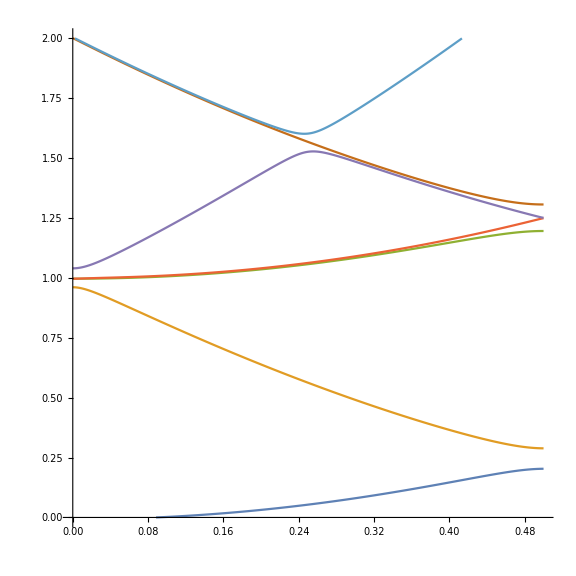

```mathematica
ListPlot[points,ImageSize->Large,Joined->True,AspectRatio->1,PlotRange->{0,2}]
```